```mathematica
W[h_,H_]:=w0+h H (v-c)/2+h(1-H)v+(1-h)H(0)+(1-h)(1-H)v/2;
```

```mathematica
dW=D[W[h,H],h]/.h->H
```

1/2 (1-H) v+1/2 H (-c+v)

```mathematica
Clear[H]
```

```mathematica
Hstart=0.1;
imax=1000;
Htab=Table[0,{i,imax}];
delta=0.01;
sub={v->1,c->3};
Htab[[1]]=Hstart;
```

```mathematica
(* dH = H + delta dW/d(H+delta) *)
```

```mathematica
For[i=2,i<imax,i++,{
Htab[[i]]=Htab[[i-1]]+delta dW/.sub/.{H->Htab[[i-1]]};
Htab[[i]]=If[Htab[[i]]>1,1,Htab[[i]]];
}];
```

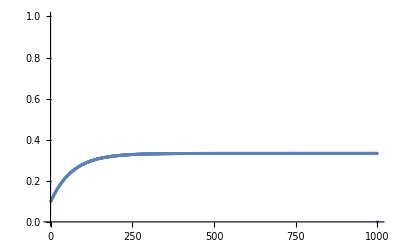

```mathematica
ListPlot[Htab,PlotRange->{All,{0,1}}]
```

```mathematica
(* try rogers model *)
```

```mathematica
QQ=(1-u)((1-P)s+P Q);
```

```mathematica
Solve[QQ==Q,Q]
```

{{Q→((-1+P) s (-1+u))/(1-P+P u)}}

```mathematica
Qhat[P_]:=((-1+P) s (-1+u))/(1-P+P u);
```

```mathematica
W[p_,P_]:=w0+p Qhat[P]b+(1-p)(s b-c);
```

```mathematica
dW=D[W[p,P],p]/.p->P
```

c-b s+(b (-1+P) s (-1+u))/(1-P+P u)

```mathematica
Pstart=0.5;
imax=1000;
Ptab=Table[0,{i,imax}];
Ptab2=Table[0,{i,imax}];
delta=0.01;
sub={b->2,c->1,s->1,u->0.1};
Ptab[[1]]=Pstart;
Ptab2[[1]]=Pstart;
```

```mathematica
For[i=2,i<imax,i++,{
Ptab[[i]]=Ptab[[i-1]]+delta dW/.sub/.{P->Ptab[[i-1]]};
Ptab[[i]]=If[Ptab[[i]]>1,1,Ptab[[i]]];
Ptab[[i]]=If[Ptab[[i]]<0,0,Ptab[[i]]];

Ptab2[[i]]=Ptab2[[i-1]]-delta dW/.sub/.{P->Ptab2[[i-1]]};
Ptab2[[i]]=If[Ptab2[[i]]>1,1,Ptab2[[i]]];
Ptab2[[i]]=If[Ptab2[[i]]<0,0,Ptab2[[i]]];
}];
```

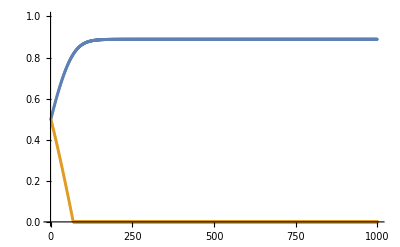

```mathematica
ListPlot[{Ptab,Ptab2},PlotRange->{All,{0,1}}]
```

```mathematica
Ptab +Ptab2
```

{0.5,0.500636,0.501272,0.501908,0.502543,0.503178,0.503812,0.504447,0.50508,0.505714,0.506347,0.506979,0.507611,0.508243,0.508874,0.509505,0.510136,0.510766,0.511396,0.512026,0.512655,0.513283,0.513912,0.514539,0.515167,0.515794,0.516421,0.517047,0.517673,0.518299,0.518924,0.519548,0.520173,0.520797,0.52142,0.522043,0.522666,0.523289,0.523911,0.524532,0.525153,0.525774,0.526394,0.527014,0.527634,0.528253,0.528872,0.52949,0.530108,0.530725,0.531343,0.531959,0.532576,0.533191,0.533807,0.534422,0.535037,0.535651,0.536265,0.536878,0.537491,0.538104,0.538716,0.539328,0.539939,0.54055,0.541161,0.541771,0.54238,0.54299,0.543598,0.544207,0.544815,0.545422,0.54603,0.546636,0.547243,0.547849,0.548454,0.549059,0.549664,0.550268,0.550872,0.551475,0.552078,0.55268,0.553283,0.553884,0.554485,0.555086,0.555686,0.556286,0.556886,0.557485,0.558084,0.558682,0.559279,0.559877,0.560474,0.56107,0.561666,0.562262,0.562857,0.563451,0.564046,0.564639,0.565233,0.565826,0.566418,0.56701,0.567602,0.568193,0.568784,0.569374,0.569964,0.570553,0.571142,0.57173,0.572318,0.572906,0.573493,0.57408,0.574666,0.575252,0.575837,0.576422,0.577006,0.57759,0.578173,0.578757,0.579339,0.579921,0.580503,0.581084,0.581665,0.582245,0.582825,0.583404,0.583983,0.584562,0.585139,0.585717,0.586294,0.586871,0.587447,0.588022,0.588598,0.589172,0.589746,0.59032,0.590894,0.591466,0.592039,0.592611,0.593182,0.593753,0.594323,0.594893,0.595463,0.596032,0.596601,0.597169,0.597736,0.598303,0.59887,0.599436,0.600002,0.600567,0.601132,0.601696,0.60226,0.602823,0.603386,0.603948,0.60451,0.605071,0.605632,0.606193,0.606753,0.607312,0.607871,0.608429,0.608987,0.609545,0.610102,0.610658,0.611214,0.611769,0.612324,0.612879,0.613433,0.613986,0.614539,0.615092,0.615644,0.616195,0.616746,0.617297,0.617847,0.618396,0.618945,0.619494,0.620042,0.620589,0.621136,0.621683,0.622229,0.622774,0.623319,0.623863,0.624407,0.624951,0.625494,0.626036,0.626578,0.627119,0.62766,0.6282,0.62874,0.62928,0.629818,0.630357,0.630894,0.631432,0.631968,0.632505,0.63304,0.633576,0.63411,0.634644,0.635178,0.635711,0.636244,0.636776,0.637307,0.637838,0.638369,0.638898,0.639428,0.639957,0.640485,0.641013,0.64154,0.642067,0.642593,0.643119,0.643644,0.644169,0.644693,0.645216,0.645739,0.646262,0.646784,0.647305,0.647826,0.648346,0.648866,0.649385,0.649904,0.650422,0.65094,0.651457,0.651974,0.65249,0.653005,0.65352,0.654034,0.654548,0.655061,0.655574,0.656086,0.656598,0.657109,0.657619,0.658129,0.658639,0.659148,0.659656,0.660164,0.660671,0.661178,0.661684,0.662189,0.662694,0.663199,0.663703,0.664206,0.664709,0.665211,0.665713,0.666214,0.666714,0.667214,0.667713,0.668212,0.668711,0.669208,0.669705,0.670202,0.670698,0.671193,0.671688,0.672182,0.672676,0.673169,0.673662,0.674154,0.674645,0.675136,0.675626,0.676116,0.676605,0.677094,0.677582,0.678069,0.678556,0.679042,0.679528,0.680013,0.680498,0.680982,0.681465,0.681948,0.68243,0.682912,0.683393,0.683873,0.684353,0.684832,0.685311,0.685789,0.686266,0.686743,0.68722,0.687696,0.688171,0.688645,0.689119,0.689593,0.690065,0.690538,0.691009,0.69148,0.691951,0.692421,0.69289,0.693358,0.693827,0.694294,0.694761,0.695227,0.695693,0.696158,0.696622,0.697086,0.697549,0.698012,0.698474,0.698936,0.699396,0.699857,0.700316,0.700775,0.701234,0.701692,0.702149,0.702606,0.703062,0.703517,0.703972,0.704426,0.70488,0.705332,0.705785,0.706237,0.706688,0.707138,0.707588,0.708037,0.708486,0.708934,0.709382,0.709828,0.710275,0.71072,0.711165,0.71161,0.712053,0.712497,0.712939,0.713381,0.713822,0.714263,0.714703,0.715142,0.715581,0.716019,0.716457,0.716894,0.71733,0.717766,0.718201,0.718635,0.719069,0.719502,0.719935,0.720367,0.720798,0.721229,0.721659,0.722088,0.722517,0.722945,0.723372,0.723799,0.724225,0.724651,0.725076,0.7255,0.725924,0.726347,0.72677,0.727191,0.727613,0.728033,0.728453,0.728872,0.729291,0.729709,0.730126,0.730543,0.730959,0.731375,0.731789,0.732204,0.732617,0.73303,0.733442,0.733854,0.734265,0.734675,0.735085,0.735494,0.735902,0.73631,0.736717,0.737123,0.737529,0.737934,0.738339,0.738743,0.739146,0.739548,0.73995,0.740352,0.740752,0.741152,0.741552,0.74195,0.742348,0.742746,0.743142,0.743539,0.743934,0.744329,0.744723,0.745116,0.745509,0.745901,0.746293,0.746684,0.747074,0.747464,0.747852,0.748241,0.748628,0.749015,0.749402,0.749787,0.750172,0.750556,0.75094,0.751323,0.751706,0.752087,0.752468,0.752849,0.753228,0.753607,0.753986,0.754364,0.754741,0.755117,0.755493,0.755868,0.756242,0.756616,0.756989,0.757362,0.757734,0.758105,0.758475,0.758845,0.759214,0.759583,0.759951,0.760318,0.760684,0.76105,0.761415,0.76178,0.762144,0.762507,0.762869,0.763231,0.763593,0.763953,0.764313,0.764672,0.765031,0.765389,0.765746,0.766102,0.766458,0.766814,0.767168,0.767522,0.767875,0.768228,0.76858,0.768931,0.769281,0.769631,0.769981,0.770329,0.770677,0.771024,0.771371,0.771717,0.772062,0.772407,0.772751,0.773094,0.773436,0.773778,0.774119,0.77446,0.7748,0.775139,0.775478,0.775816,0.776153,0.776489,0.776825,0.777161,0.777495,0.777829,0.778162,0.778495,0.778827,0.779158,0.779489,0.779818,0.780148,0.780476,0.780804,0.781131,0.781458,0.781784,0.782109,0.782434,0.782757,0.783081,0.783403,0.783725,0.784046,0.784367,0.784687,0.785006,0.785325,0.785642,0.78596,0.786276,0.786592,0.786907,0.787222,0.787536,0.787849,0.788162,0.788474,0.788785,0.789095,0.789405,0.789714,0.790023,0.790331,0.790638,0.790945,0.791251,0.791556,0.791861,0.792164,0.792468,0.79277,0.793072,0.793374,0.793674,0.793974,0.794273,0.794572,0.79487,0.795167,0.795464,0.79576,0.796055,0.79635,0.796644,0.796937,0.79723,0.797522,0.797813,0.798104,0.798394,0.798683,0.798972,0.79926,0.799548,0.799834,0.80012,0.800406,0.800691,0.800975,0.801258,0.801541,0.801823,0.802105,0.802386,0.802666,0.802945,0.803224,0.803502,0.80378,0.804057,0.804333,0.804609,0.804884,0.805158,0.805432,0.805705,0.805977,0.806249,0.80652,0.80679,0.80706,0.807329,0.807598,0.807866,0.808133,0.808399,0.808665,0.80893,0.809195,0.809459,0.809722,0.809985,0.810247,0.810508,0.810769,0.811029,0.811289,0.811548,0.811806,0.812063,0.81232,0.812576,0.812832,0.813087,0.813341,0.813595,0.813848,0.814101,0.814352,0.814604,0.814854,0.815104,0.815353,0.815602,0.81585,0.816097,0.816344,0.81659,0.816836,0.817081,0.817325,0.817568,0.817811,0.818054,0.818295,0.818536,0.818777,0.819017,0.819256,0.819495,0.819732,0.81997,0.820207,0.820443,0.820678,0.820913,0.821147,0.821381,0.821614,0.821846,0.822078,0.822309,0.82254,0.82277,0.822999,0.823228,0.823456,0.823683,0.82391,0.824136,0.824362,0.824587,0.824811,0.825035,0.825258,0.825481,0.825703,0.825924,0.826145,0.826365,0.826585,0.826804,0.827022,0.82724,0.827457,0.827674,0.82789,0.828105,0.82832,0.828534,0.828748,0.828961,0.829173,0.829385,0.829596,0.829807,0.830017,0.830226,0.830435,0.830643,0.830851,0.831058,0.831265,0.83147,0.831676,0.831881,0.832085,0.832288,0.832491,0.832694,0.832896,0.833097,0.833297,0.833498,0.833697,0.833896,0.834094,0.834292,0.834489,0.834686,0.834882,0.835078,0.835273,0.835467,0.835661,0.835854,0.836047,0.836239,0.83643,0.836621,0.836812,0.837002,0.837191,0.83738,0.837568,0.837755,0.837943,0.838129,0.838315,0.8385,0.838685,0.838869,0.839053,0.839236,0.839419,0.839601,0.839783,0.839964,0.840144,0.840324,0.840503,0.840682,0.84086,0.841038,0.841215,0.841392,0.841568,0.841744,0.841919,0.842093,0.842267,0.84244,0.842613,0.842786,0.842957,0.843129,0.8433,0.84347,0.843639,0.843809,0.843977,0.844145,0.844313,0.84448,0.844647,0.844813,0.844978,0.845143,0.845308,0.845472,0.845635,0.845798,0.84596,0.846122,0.846284,0.846445,0.846605,0.846765,0.846924,0.847083,0.847241,0.847399,0.847557,0.847713,0.84787,0.848025,0.848181,0.848336,0.84849,0.848644,0.848797,0.84895,0.849102,0.849254,0.849406,0.849556,0.849707,0.849857,0.850006,0.850155,0.850303,0.850451,0.850599,0.850746,0.850892,0.851038,0.851184,0.851329,0.851473,0.851618,0.851761,0.851904,0.852047,0.852189,0.852331,0.852472,0.852613,0.852753,0.852893,0.853033,0.853172,0.85331,0.853448,0.853586,0.853723,0.853859,0.853996,0.854131,0.854266,0.854401,0.854536,0.85467,0.854803,0.854936,0.855068,0.855201,0.855332,0.855463,0.855594,0.855724,0.855854,0.855984,0.856113,0.856241,0.856369,0.856497,0.856624,0.856751,0.856877,0.857003,0.857129,0.857254,0.857378,0.857503,0.857626,0.85775,0.857873,0.857995,0.858117,0.858239,0.85836,0.858481,0.858601,0.858721,0.858841,0.85896,0.859078,0.859197,0.859315,0.859432,0.859549,0.859666,0.859782,0.859898,0.860013,0.860128,0.860243,0.860357,0.860471,0.860584,0.860697,0.86081,0.860922,0.861034,0.861145,0.861256,0.861367,0.861477,0.861587,0.861696,0.861805,0.861914,0.862022,0.86213,0.862237,0.862344,0.862451,0.862557,0.862663,0.862769,0.862874,0.862979,0.863083,0.863187,0.863291,0.863394,0.863497,0.8636,0.863702,0.863804,0.863905,0.864006,0.864107,0.864207,0.864307,0.864407,0.864506,0.864605,0.864703,0.864802,0.864899,0.864997,0.865094,0.865191,0.865287,0.865383,0.865479,0.865574,0.865669,0.865763,0.865858,0.865952,0.866045,0.866138,0.866231,0.866324,0}